#### Find the closest path between two elastic maps INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook Variables to change: Tmat, dt, ListSigma

#### choose Tmat

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrown;
```

#### check that it’s symmetric, display info

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

#### Find closest T to ISO

```mathematica
WantDetails="WantDetails";
```

```mathematica
OutputFor[Tmat,ISO]
```

```mathematica
betaISO =βTinitial[Tmat,ISO]/Degree  (* AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree *)
TISO =Closest[Tmat,ISO];  (* ProjToVSigOfU[Tmat,id,ISO]*)
MatrixForm[TISO]
```

#### Matrix norms (not used, but worth thinking about)

```mathematica
Ntriv =Norm[Tmat,Frobenius]
Niso =Norm[TISO,Frobenius]
Norm[TISO/Niso,Frobenius]
Norm[Ntriv/Ntriv,Frobenius]
```

#### check: the angle does not depend on the size of the T

```mathematica
AngleMatrix[Tmat,TISO]/Degree
AngleMatrix[Tmat/Ntriv,TISO/Niso]/Degree
```

#### Choose Tmat1 and Tmat2

```mathematica
Tmat1 =TISO;
Tmat2 =Tmat;
```

#### Example: TET to XISO segment for the Brown map (set ListSigma={TET,XISO} below) Here TXISO is the closest to TRIV (Pathway 2), and β_XISO = 20.35^o

```mathematica
OutputFor[Tmat,TET]
TTET=Closest[Tmat,TET];
OutputFor[Tmat,XISO]
TXISO=Closest[Tmat,XISO];
Tmat1 =TXISO;
Tmat2 =TTET;
MatrixForm[TXISO]
```

#### Example: TET to XISO segment for the Brown map (set ListSigma={TET,XISO} below) Here TXISO is the closest to TTET (Pathway 3), and β_XISO = 18.58^o (which is less than Pathway 2, as expected)

```mathematica
(* OutputFor[Tmat,TET]
TTET=Closest[Tmat,TET];
OutputFor[TTET,XISO]
TXISO=Closest[TTET,XISO];   (* note TTET instead of Tmat *)
Tmat1 =TXISO;
Tmat2 =TTET;
MatrixForm[TXISO] *)
```

#### KEY FUNCTION

```mathematica
TT[t_,Tmat1_,Tmat2_]:=(1-t) Tmat1+t Tmat2
```

#### check endpoints (but not that your chosen t values may exclude the endpoints)

```mathematica
MatrixForm[Tmat1]
MatrixForm[TT[0,Tmat1,Tmat2]]
MatrixForm[Tmat2]
MatrixForm[TT[1,Tmat1,Tmat2]]
```

#### t values to use

```mathematica
t1 = 1; t2=1.1;dt =0.01;   (* Igel -- show that t > 1 *)
t1 = 0; t2=1;
dt =0.5;
dt = 0.02;
Ranget=Range[t1,t2,dt]
```

```mathematica
t1 = 0.42; t2 = 0.44;dt=0.005;  (* Brown TET triangle - Pathway 2 *)
(* t1 = 0.38; t2 = 0.40;dt = 0.005; *)  (* Brown TET triangle - Pathway 3 *)
Ranget=Join[{0},Range[t1,t2,dt],{1}]
```

#### Display the set of Tmats as BB and as Voigt

```mathematica
(Print["t = ",# ]; PrintVoigt[TT[#,Tmat1,Tmat2]])&/@Ranget
```

## Optional: Choose an orientation for all the balls based on the closest XISO (or whatever you want).

#### commands copied from LatticeOfClosestMaps.nb Display the set of REORIENTED Tmats as BB and as Voigt

```mathematica
(* WantDetails="WantDetails";
OutputFor[Tmat,XISO]
MatrixForm[UT[Tmat,XISO]]
MatrixForm[Closest[Tmat,XISO]]
OutputFor[Closest[Tmat,XISO],XISO]
Ux=IdentityMatrix[3];
(* Ux=UT[Closest[Tmat,XISO],XISO]; *)
MatrixForm[Ux]
Ubarx=MatrixUbar[Ux];
MatrixForm[Chop[Ubarx,.0001]]
(Print["t = ",# ]; PrintVoigt[Transpose[Ubarx].TT[#,Tmat1,Tmat2].Ubarx])&/@Ranget *)
```

## Proceed with Tmat in its original orientation

```mathematica
Ux=IdentityMatrix[3];
Ubarx=MatrixUbar[Ux];
```

## Set of Sigmas to use

#### MONO is needed if you want to plot the balls

```mathematica
ListSigma={TRIV,MONO,TRIG,ORTH,TET,CUBE,XISO,ISO};
```

```mathematica
ListSigma={ORTH,TET};
```

```mathematica
ListSigma={MONO,XISO,TET}; (* Brown triangle *)
```

## Example functions (none of these are needed)

#### Example of plotting two sets of points on one plot.

```mathematica
f[t_,Sigma_]:=t/2
```

```mathematica
Graphics[{PointSize[.02],
Table[Point[{t,0}],                    {t,.2,.8,.2}],
Table[Point[{t,f[t,XISO]}],{t,.2,.8,.2}],
Table[Point[{t,f[t,ORTH]}],{t,.2,.8,.2}]},Axes->True,AxesOrigin->{0,0}]
```

#### Example: Closest to MONO for t=0.2

```mathematica
Ttest =TT[0.2,Tmat1,Tmat2];
MatrixForm[Ttest]
OutputFor[Ttest,MONO]
```

#### This is the rotation from the minimization.

```mathematica
(* UT[Tmat,Σ] *)
```

#### This is the corresponding elastic map.

```mathematica
(* MatrixForm[ProjToVSigOfU[Tmat,UT[Tmat,Σ],Σ]] *)
```

#### This command is in the common_funs file.

```mathematica
(* Closest[Tmat_,Sigma_]:=ProjToVSigOfU[Tmat,UT[Tmat,Sigma],Sigma]; *)
```

#### This is the angle between Tmat and the closest Sigma map.

```mathematica
(* AngleMatrix[Tmat,Closest[Tmat,Sigma]] *)
```

#### This is the first matrix in OutputFor

```mathematica
MatrixForm[UT[Ttest,MONO]]
```

#### This is the last matrix in OutputFor (Closest[Tmat,Sigma] is defined in common_funs.nb)

```mathematica
MatrixForm[Closest[Ttest,MONO]]
```

#### These are the βs in OutputFor

```mathematica
AngleMatrix[Ttest,Closest[Ttest,MONO]]/Degree
```

## Calculate distance to each symmetry class KEY COMMAND: OutputFor performs the key calculations (minimizations)

```mathematica
WantDetails="NoWantDetails";
```

```mathematica
Ranget
```

```mathematica
ListSigma
```

```mathematica
(* Table[OutputFor[TT[t,Tmat1,Tmat2],#]&/@ListSigma,{t,t1,t2,dt}] *)
```

```mathematica
(* Do[(Print["t = ",t];
OutputFor[TT[t,Tmat1,Tmat2],#])&/@ListSigma,{i,t1,t2,dt}] *)
```

```mathematica
(* OutputFor[TT[Ranget[[1]],Tmat1,Tmat2],ListSigma[[1]]] *) (* example of one OutpurFor *)
```

```mathematica
Do[(Print["t = ",Ranget[[i]]];OutputFor[TT[Ranget[[i]],Tmat1,Tmat2],#])&/@ListSigma,{i,1,Length[Ranget]}]
```

## Optional: Plot the balls

```mathematica
eye=10xyzTP[{30Degree,75Degree}];
contours[Tmat]=Range[0,27,3];
MaxForScaling[Tmat]=27.5;
plotpoints=10;
```

#### MDFgraphics is in common_funs.db -- this plots hemispheres

```mathematica
(* Ranget
MDFgraphics[{0,0,0},1,TT[#,Tmat1,Tmat2],eye,contours[Tmat],MaxForScaling[Tmat],plotpoints,{}]&/@Ranget
MDFgraphics[{0,0,0},1,Closest[TT[#,Tmat1,Tmat2],TET],eye,contours[Tmat],MaxForScaling[Tmat],plotpoints,{}]&/@Ranget
MDFgraphics[{0,0,0},1,Closest[TT[#,Tmat1,Tmat2],XISO],eye,contours[Tmat],MaxForScaling[Tmat],plotpoints,{}]&/@Ranget *)
```

#### cpMONO is in common_funs.nb; it requires defining the contours

```mathematica
contours[Tmat]=Range[0,20,2]
MaxForScaling[Tmat]=20
```

```mathematica
(* Show[cpMONO[TT[Ranget[[1]],Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye] *)
```

#### function for plotting the U matrix (columns)

```mathematica
Udots[Tmat_,Sigma_]:=Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.03],{ 
{Red,     Point[UT[Tmat, Sigma].{1,0,0}],Point[UT[Tmat, Sigma].{-1,0,0}]},
{Blue,   Point[UT[Tmat, Sigma].{0,1,0}],Point[UT[Tmat, Sigma].{0,-1,0}]},
{Green,Point[UT[Tmat, Sigma].{0,0,1}],Point[UT[Tmat, Sigma].{0,0,-1}]}}},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

#### main plot

```mathematica
Ranget 
Udots[TT[#,Tmat1,Tmat2],MONO]&/@Ranget
Show[cpMONO[TT[#,Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye] &/@Ranget
Udots[TT[#,Tmat1,Tmat2],TET]&/@Ranget
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],TET],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye] &/@Ranget
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],XISO],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye] &/@Ranget
```

## Beta curves

#### Angle between Tmat and the closest-Sigma to Tmat

```mathematica
f[Tmat_,Sigma_]:=MakeReal[AngleMatrix[Tmat,Closest[Tmat,Sigma]]/Degree];
```

#### Plot all the beta curves together. (With the Closest maps pre-saved, the plotting should be quick.)

```mathematica
ListSigma
```

```mathematica
line[Sigma_]:=Line[{#,f[TT[#,Tmat1,Tmat2],Sigma]}&/@Ranget];
```

#### Brown triangle (custom commands)

```mathematica
Graphics[{PointSize[.04],
line/@ListSigma,
{ColorData["Rainbow"][2/6],Point[{#,f[TT[#,Tmat1,Tmat2],  TET]}]&/@Ranget},
{ColorData["Rainbow"][4/6],Point[{#,f[TT[#,Tmat1,Tmat2],XISO]}]&/@Ranget}
},Axes->True,AspectRatio->1]
```

#### This simple plot should always work

```mathematica
Graphics[line/@ListSigma,Axes->True,AspectRatio->1]
```

#### This fancier version with colored dots will require having run the full set for ListSigma. It will generate figures like the ones saved below.

```mathematica
(* Graphics[{PointSize[.02],
line/@ListSigma,
{ColorData["Rainbow"][0/6],Point[{#,f[TT[#,Tmat1,Tmat2],MONO]}]&/@Ranget},
{ColorData["Rainbow"][1/6],Point[{#,f[TT[#,Tmat1,Tmat2],ORTH]}]&/@Ranget},
{ColorData["Rainbow"][2/6],Point[{#,f[TT[#,Tmat1,Tmat2],  TET]}]&/@Ranget},
{ColorData["Rainbow"][3/6],Point[{#,f[TT[#,Tmat1,Tmat2],TRIG]}]&/@Ranget},
{ColorData["Rainbow"][4/6],Point[{#,f[TT[#,Tmat1,Tmat2],XISO]}]&/@Ranget},
{ColorData["Rainbow"][5/6],Point[{#,f[TT[#,Tmat1,Tmat2],CUBE]}]&/@Ranget},
{ColorData["Rainbow"][6/6],Point[{#,f[TT[#,Tmat1,Tmat2],  ISO]}]&/@Ranget},
Point[{#,0}]&/@Ranget,Point[{1,0}],
Text[Style[#,13],{t2+.03,f[TT[t2,Tmat1,Tmat2],#]},{-1,0}]&/@ListSigma},Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->500] *)
```

## For reference (Tmat1 = ISO, Tmat2 = TRIV unless otherwise noted)

#### Igel: dt = 0.5, ListSigma = {ORTH, TET}

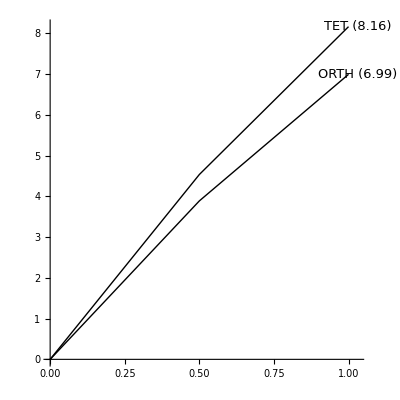

#### Brown: dt = 0.02, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET} (We did not expect to see such a non-differentiable curve.)

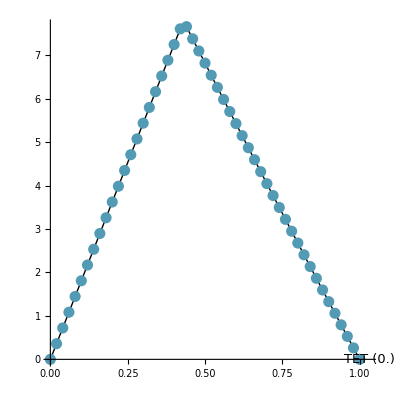

#### Brown: dt = 0.005, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET,XISO} t1 = 0.41, t2 = 0.45

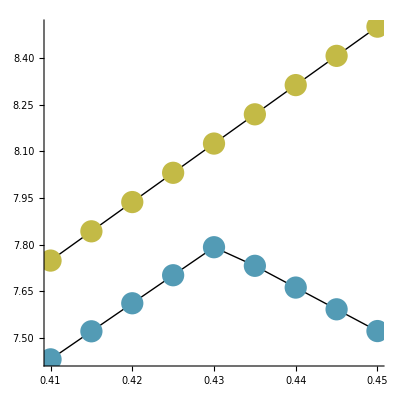

#### Brown: dt = 0.005, Tmat1=closest(TTET,XISO), Tmat2=TTET, ListSigma = {TET,XISO} t1 = 0.38, t2 = 0.40

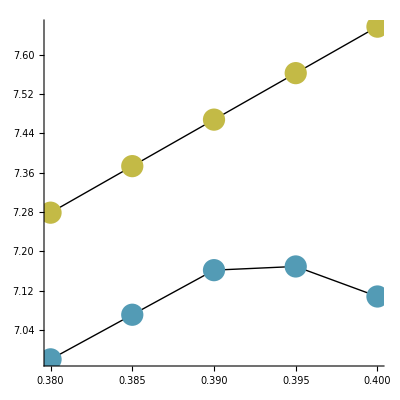

#### Igel: dt = 0.1, ListSigma = all

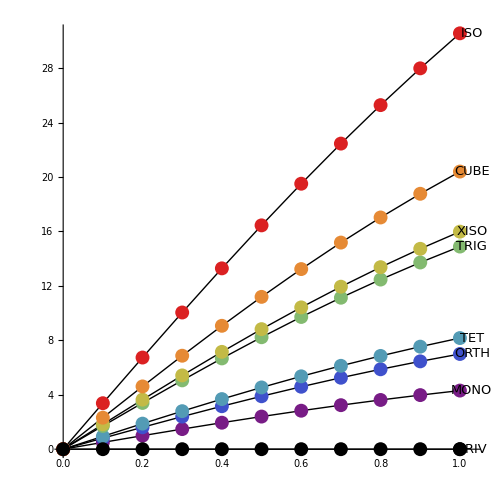

#### TmatMar17: dt = 0.1, ListSigma = all

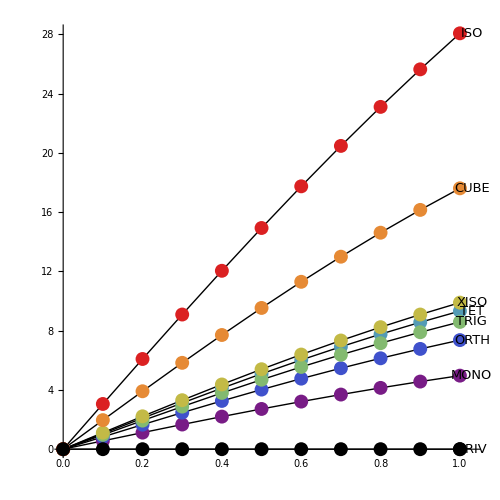

#### TmatBrown: dt = 0.1, ListSigma = all